{{Potential,Energy,Kinetic,Energy,Total,Energy,Velocity,Position,time},{0.51005,0.5,1.01005,1.,1.01,0.},{0.520097,0.489953,1.01005,0.989902,1.0199,0.01},{0.530137,0.479904,1.01004,0.979698,1.0297,0.02},{0.540166,0.469866,1.01003,0.969398,1.03939,0.03},{0.55018,0.459843,1.01002,0.959003,1.04898,0.04},{0.560174,0.449838,1.01001,0.948513,1.05847,0.05},{0.570146,0.439853,1.01,0.937927,1.06784,0.06},{0.58009,0.429892,1.00998,0.927246,1.07712,0.07},{0.590004,0.419958,1.00996,0.916469,1.08628,0.08},2482,{0.292981,0.716652,1.00963,1.19721,0.765482,24.91},{0.302158,0.707519,1.00968,1.18955,0.777377,24.92},{0.311415,0.698304,1.00972,1.18178,0.789195,24.93},{0.320748,0.689008,1.00976,1.17389,0.800934,24.94},{0.330154,0.679637,1.00979,1.16588,0.812593,24.95},{0.339629,0.670198,1.00983,1.15776,0.824171,24.96},{0.349169,0.660688,1.00986,1.14951,0.835666,24.97},{0.35877,0.651117,1.00989,1.14116,0.847077,24.98},{0.368429,0.641488,1.00992,1.13269,0.858404,24.99}}
 |  |  |  |

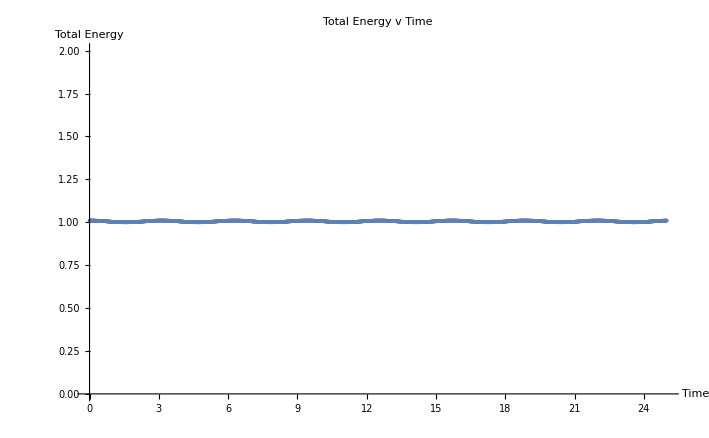

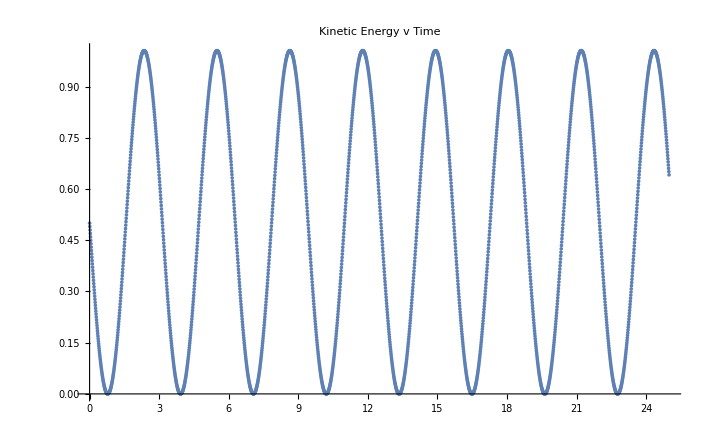

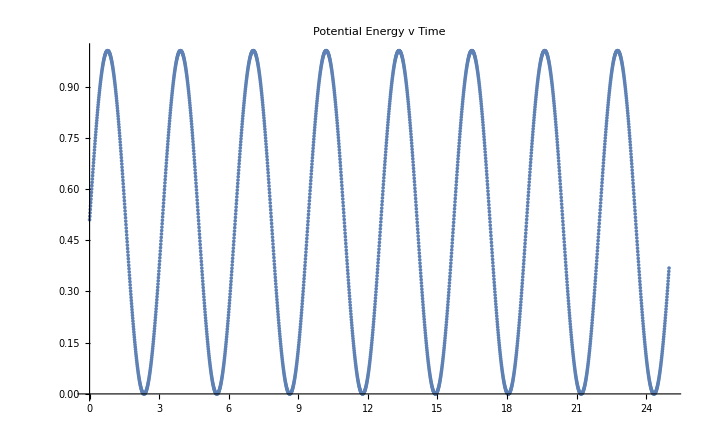

```mathematica
data = Import["/Users/masauer2/urban-doodle/output.txt", "Table"]
data = Drop[data,1];
totalenergy = data[[All,3]];
time = data[[All,6]];
ListPlot[Transpose@{y,x}, PlotRange->{0,2}, AxesLabel->{"Time", "Total Energy"}, PlotLabel->"Total Energy v Time"] (*Total Energy v Time*)
ListPlot[Transpose@{data[[All,6]],data[[All,2]]}, PlotLabel->"Kinetic Energy v Time"] (*Kinetic Energy v Time*)
ListPlot[Transpose@{data[[All,6]],data[[All,1]]}, PlotLabel->"Potential Energy v Time"](*Potential Energy v Time*)
```